# Export a .tgf graph

Madeleine King
CSC253 Spring 2022

## Paths

```mathematica
OUTPUTDIRU=NotebookDirectory[]<>"../Data/UGraphs/";
```

```mathematica
OUTPUTDIRD=NotebookDirectory[]<>"../Data/DGraphs/";
```

# Create, Export, Visualize a Graph

```mathematica
UEDGES01={0<->1,1<->2,2<->3,1<->3,0<->2,1<->4};
UGRAPH01=Graph[Range[0,5],UEDGES01];
Export[OUTPUTDIRU<>"graph01.tgf",UGRAPH01];
```

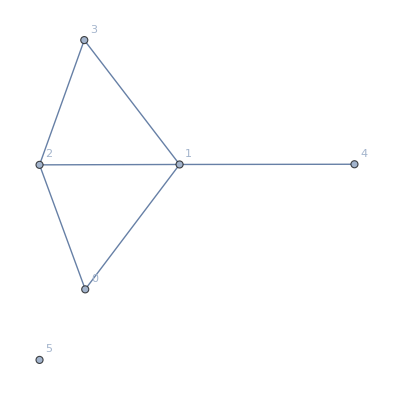

```mathematica
SetProperty[UGRAPH01,VertexLabels->Automatic]
```

```mathematica
UEDGES0={0<->1,0<->2,2<->3,2<->4, 1<->5, 1<->6};
UGRAPH0=Graph[Range[0,6],UEDGES0];
```

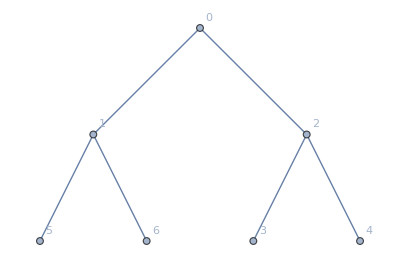

```mathematica
SetProperty[UGRAPH0,VertexLabels->Automatic]
```

```mathematica
Export[OUTPUTDIRU<>"mygraph0.tgf",UGRAPH0];
```

```mathematica
DEDGES1={0->1,0->2,2->3,2->4, 5->1, 1->6, 7->8, 3->4, 4->0, 6->5, 8->9, 9->7};
DGRAPH1=Graph[Range[0,6],DEDGES1];
```

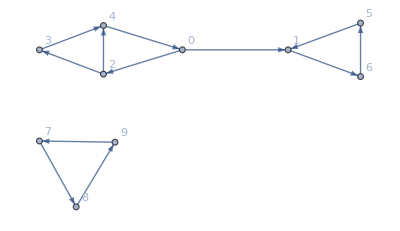

```mathematica
SetProperty[DGRAPH1,VertexLabels->Automatic]
```

```mathematica
Export[OUTPUTDIRD<>"dgraphStrongComps.tgf",DGRAPH1];
```

```mathematica
DEDGES4={0->1, 0->2, 2->1, 1->3};
DGRAPH4=Graph[Range[0,3],DEDGES4];
```

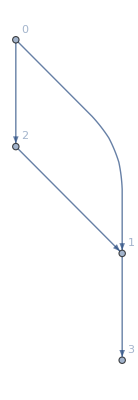

```mathematica
SetProperty[DGRAPH4,VertexLabels->Automatic]
```

```mathematica
Export[OUTPUTDIRD<>"dgraphdag.tgf",DGRAPH4];
```

```mathematica
DEDGES2={2->0,2->3, 5->1, 1->6,  3->4, 4->0, 6->5};
DGRAPH2=Graph[Range[0,6],DEDGES2];
```

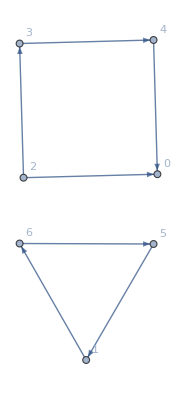

```mathematica
SetProperty[DGRAPH2,VertexLabels->Automatic]
```

```mathematica
Export[OUTPUTDIRD<>"dgraphNoStrongComps.tgf",DGRAPH2];
```

```mathematica
DEDGES3={0->2,2->3,3->4, 4->0, 2->1};
DGRAPH3=Graph[Range[0,4],DEDGES3];
```

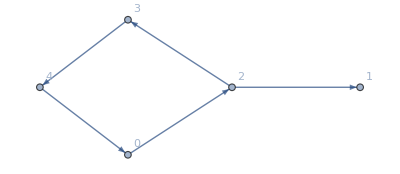

```mathematica
SetProperty[DGRAPH3,VertexLabels->Automatic]
```

```mathematica
Export[OUTPUTDIRD<>"dgraphStrong.tgf",DGRAPH3];
```

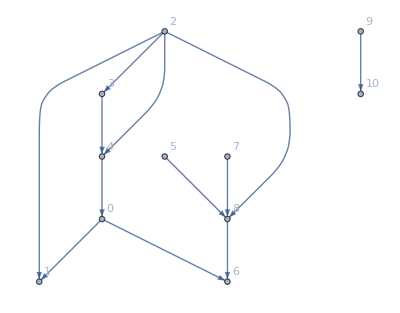

```mathematica
DEDGES5={2->3,3->4, 4->0, 2->1, 0->1, 7->8, 8->6, 5->8, 2->4, 2->8, 9-> 10, 0->6};
DGRAPH5=Graph[Range[0,10],DEDGES5];
SetProperty[DGRAPH5,VertexLabels->Automatic]
```

```mathematica
Export[OUTPUTDIRD<>"dgraphComplicated.tgf",DGRAPH5];
```